```mathematica
SetDirectory["/Users/tanjona/Box Sync/projects/corona_mada/"];
```

#### Basic settings

```mathematica
(* from R brewer *)
code ={{0,0,0},{90,60,0},{35,70,90},{0,60,50},{95,90,25},{0,45,70},{80,40,0},{80,60,70}}/100;
col =RGBColor[#[[1]],#[[2]],#[[3]]]&/@code
```

{RGBColor[0, 0, 0],RGBColor[Rational[9, 10], Rational[3, 5], 0],RGBColor[Rational[7, 20], Rational[7, 10], Rational[9, 10]],RGBColor[0, Rational[3, 5], Rational[1, 2]],RGBColor[Rational[19, 20], Rational[9, 10], Rational[1, 4]],RGBColor[0, Rational[9, 20], Rational[7, 10]],RGBColor[Rational[4, 5], Rational[2, 5], 0],RGBColor[Rational[4, 5], Rational[3, 5], Rational[7, 10]]}

```mathematica
cb1 = {{255,255,204},{255,237,160},{254,217,118},{254,178,76},{253,141,60},{252,78,42},{227,26,28},{189,0,38},{128,0,38}}/255;
cbcol1 = RGBColor[#[[1]],#[[2]],#[[3]]]&/@cb1
```

{RGBColor[1, 1, Rational[4, 5]],RGBColor[1, Rational[79, 85], Rational[32, 51]],RGBColor[Rational[254, 255], Rational[217, 255], Rational[118, 255]],RGBColor[Rational[254, 255], Rational[178, 255], Rational[76, 255]],RGBColor[Rational[253, 255], Rational[47, 85], Rational[4, 17]],RGBColor[Rational[84, 85], Rational[26, 85], Rational[14, 85]],RGBColor[Rational[227, 255], Rational[26, 255], Rational[28, 255]],RGBColor[Rational[63, 85], 0, Rational[38, 255]],RGBColor[Rational[128, 255], 0, Rational[38, 255]]}

```mathematica
cb2 = Partition[{255,245,235,254,230,206,253,208,162,253,174,107,253,141,60,241,105,19,217,72,1,166,54,3,127,39,4},3]/255;
cbcol2 = RGBColor[#[[1]],#[[2]],#[[3]]]&/@cb2
```

{RGBColor[1, Rational[49, 51], Rational[47, 51]],RGBColor[Rational[254, 255], Rational[46, 51], Rational[206, 255]],RGBColor[Rational[253, 255], Rational[208, 255], Rational[54, 85]],RGBColor[Rational[253, 255], Rational[58, 85], Rational[107, 255]],RGBColor[Rational[253, 255], Rational[47, 85], Rational[4, 17]],RGBColor[Rational[241, 255], Rational[7, 17], Rational[19, 255]],RGBColor[Rational[217, 255], Rational[24, 85], Rational[1, 255]],RGBColor[Rational[166, 255], Rational[18, 85], Rational[1, 85]],RGBColor[Rational[127, 255], Rational[13, 85], Rational[4, 255]]}

```mathematica
cb3 = Partition[{247,251,255,222,235,247,198,219,239,158,202,225,107,174,214,66,146,198,33,113,181,8,81,156,8,48,107},3]/255;
cbcol3 = RGBColor[#[[1]],#[[2]],#[[3]]]&/@cb3
```

{RGBColor[Rational[247, 255], Rational[251, 255], 1],RGBColor[Rational[74, 85], Rational[47, 51], Rational[247, 255]],RGBColor[Rational[66, 85], Rational[73, 85], Rational[239, 255]],RGBColor[Rational[158, 255], Rational[202, 255], Rational[15, 17]],RGBColor[Rational[107, 255], Rational[58, 85], Rational[214, 255]],RGBColor[Rational[22, 85], Rational[146, 255], Rational[66, 85]],RGBColor[Rational[11, 85], Rational[113, 255], Rational[181, 255]],RGBColor[Rational[8, 255], Rational[27, 85], Rational[52, 85]],RGBColor[Rational[8, 255], Rational[16, 85], Rational[107, 255]]}

```mathematica
cbcol4 =  RGBColor[#[[1]],#[[2]],#[[3]]]&/@(Partition[{247,252,245,229,245,224,199,233,192,161,217,155,116,196,118,65,171,93,35,139,69,0,109,44,0,68,27},3]/255)
```

{RGBColor[Rational[247, 255], Rational[84, 85], Rational[49, 51]],RGBColor[Rational[229, 255], Rational[49, 51], Rational[224, 255]],RGBColor[Rational[199, 255], Rational[233, 255], Rational[64, 85]],RGBColor[Rational[161, 255], Rational[217, 255], Rational[31, 51]],RGBColor[Rational[116, 255], Rational[196, 255], Rational[118, 255]],RGBColor[Rational[13, 51], Rational[57, 85], Rational[31, 85]],RGBColor[Rational[7, 51], Rational[139, 255], Rational[23, 85]],RGBColor[0, Rational[109, 255], Rational[44, 255]],RGBColor[0, Rational[4, 15], Rational[9, 85]]}

```mathematica
cbcol5 =  RGBColor[#[[1]],#[[2]],#[[3]]]&/@(Partition[{255,245,240,254,224,210,252,187,161,252,146,114,251,106,74,239,59,44,203,24,29,165,15,21,103,0,13},3]/255)
```

{RGBColor[1, Rational[49, 51], Rational[16, 17]],RGBColor[Rational[254, 255], Rational[224, 255], Rational[14, 17]],RGBColor[Rational[84, 85], Rational[11, 15], Rational[161, 255]],RGBColor[Rational[84, 85], Rational[146, 255], Rational[38, 85]],RGBColor[Rational[251, 255], Rational[106, 255], Rational[74, 255]],RGBColor[Rational[239, 255], Rational[59, 255], Rational[44, 255]],RGBColor[Rational[203, 255], Rational[8, 85], Rational[29, 255]],RGBColor[Rational[11, 17], Rational[1, 17], Rational[7, 85]],RGBColor[Rational[103, 255], 0, Rational[13, 255]]}

```mathematica
cbcol6 =  RGBColor[#[[1]],#[[2]],#[[3]]]&/@(Partition[{252,251,253,239,237,245,218,218,235,188,189,220,158,154,200,128,125,186,106,81,163,84,39,143,63,0,125},3]/255)
```

{RGBColor[Rational[84, 85], Rational[251, 255], Rational[253, 255]],RGBColor[Rational[239, 255], Rational[79, 85], Rational[49, 51]],RGBColor[Rational[218, 255], Rational[218, 255], Rational[47, 51]],RGBColor[Rational[188, 255], Rational[63, 85], Rational[44, 51]],RGBColor[Rational[158, 255], Rational[154, 255], Rational[40, 51]],RGBColor[Rational[128, 255], Rational[25, 51], Rational[62, 85]],RGBColor[Rational[106, 255], Rational[27, 85], Rational[163, 255]],RGBColor[Rational[28, 85], Rational[13, 85], Rational[143, 255]],RGBColor[Rational[21, 85], 0, Rational[25, 51]]}

```mathematica
(* Base plot formatting *)
as = AxesStyle->Directive[Black, AbsoluteThickness[1]];
ls = LabelStyle->Directive[16,Black, FontFamily-> "Helvetica"];
fs = FrameStyle->Directive[Black,AbsoluteThickness[1]];
is = ImageSize->350;
```

## Hard-coded multinomial implementation (from Stack exchange)

```mathematica
(* alternative implementation of multinomial, faster when N large and pp vary *)
ablRanBinGeom=Compile[{{n,_Integer},{p,_Real}},Module[{y=0,x=0,comp=0,er,v,scale=0.0},If[p≥1.0,Return[n]];
If[p≤0.5,comp=0;scale=-1.0/Internal`Log1p[-p],comp=1;
scale=-1.0/Log[p]];
While[True,er=-Log[RandomReal[]];
v=er*scale;
If[v>n,Break[]];
y=y+Ceiling[v];
If[y>n,Break[]];
x=x+1;];
If[comp==1,n-x,x]],CompilationTarget->"C",RuntimeAttributes->{Listable}];
ablRanBinBtpe=Compile[{{n,_Integer},{p,_Real}},Module[{comp=0,r,q,nrq,fM,M,Mi,p1,xM,xL,xR,c,a,lamL,lamR,p2,p3,p4,y,u,v,x,k,S,F,t,A,x1,f1,z,w,rho},If[p≥1.0,Return[n]];
If[p≤0.5,comp=0;r=p;q=1.0-p,comp=1;r=1.0-p;q=p];
nrq=n*r*q;
fM=(n+1)*r;
M=Floor[fM];
Mi=Floor[M];
p1=Floor[2.195*Sqrt[nrq]-4.6*q]+0.5;
xM=M+0.5;
xL=xM-p1;
xR=xM+p1;
c=0.134+20.5/(15.3+M);
a=(fM-xL)/(fM-xL*r);
lamL=a*(1.0+0.5*a);
a=(xR-fM)/(xR*q);
lamR=a*(1.0+0.5*a);
p2=p1*(1.0+2.0*c);
p3=p2+c/lamL;
p4=p3+c/lamR;
y=0;
While[True,(*Step 1*)u=p4*RandomReal[];
v=RandomReal[];
Which[u≤p1,y=Floor[xM-p1*v+u];
Break[],u≤p2,(*Step 2*)x=xL+(u-p1)/c;
v=v*c+1.0-Abs[M-x+0.5]/p1;
If[v>1,Continue[]];
y=Floor[x],u≤p3,(*Step 3*)y=Floor[xL+Log[v]/lamL];
If[y<0,Continue[]];
v=v*(u-p2)*lamL,True,(*Step 4*)y=Floor[xR-Log[v]/lamR];
If[y>n,Continue[]];
v=v*(u-p3)*lamR];
A=Log[v];
If[A>(LogGamma[Mi+1]+LogGamma[n-Mi+1]+LogGamma[y+1]+LogGamma[n-y+1]+(y-Mi)*Log[r/q]),Continue[]];
Break[];];
If[comp==1,n-y,y]],CompilationTarget->"C",CompilationOptions->{"InlineExternalDefinitions"->True},RuntimeAttributes->{Listable}];

ablRanBinomial=Compile[{{n,_Integer},{p,_Real}},Module[{q=1.0-p},If[n*Min[p,q]>20,ablRanBinBtpe[n,p],ablRanBinGeom[n,p]]],CompilationTarget->"C",CompilationOptions->{"InlineExternalDefinitions"->True},RuntimeAttributes->{Listable}];

ablRanMultinomial=Compile[{{n,_Integer},{p,_Real,1}},Module[{k=Length[p],rp,i,km1,cn,pi,xi,x},rp=1.0;cn=n;
i=0;
km1=k-1;
x=Table[0,{k}];
While[i<km1&&cn>0,i+=1;
pi=p[[i]];
If[pi<rp,xi=ablRanBinomial[cn,pi/rp];
x[[i]]=xi;
cn-=xi;
rp-=pi;,x[[i]]=cn;
cn=0];];
If[i==km1,x[[k]]=cn,Do[x[[j]]=0,{j,i+1,k}]];
x],CompilationTarget->"C",CompilationOptions->{"InlineExternalDefinitions"->True},RuntimeAttributes->{Listable}];
```

```mathematica
SimMobility[ popD_,mobMatrix_,diagReg_,param_,time_,rep_]:= Module[{res,NCITY = 22, Nx, Sx, Ex, Ix, Rx, oSx, oEx, oIx, oRx,mB,rB, rA, rG,SMov, EMov, IMov,RMov,nI, nIID, freqState, mvState, mvTOTAL, mv, BB, AA,GG},
Nx = popD;
SeedRandom[rep];
Sx =Nx;
nI = 20;
nIID = 1;
Ex = ConstantArray[0, NCITY]; 
Ix = ConstantArray[0, NCITY];
Rx = ConstantArray[0, NCITY];
Ix[[nIID ]]=nI;
Sx[[nIID]] =Nx[[nIID]] - Ix[[nIID]];
res = ConstantArray[{Sx, Ex, Ix, Rx}, time];

(* model parameters *)
mvTOTAL = diagReg; (* number of people moving out of each region every day*)
mv = mobMatrix;

BB = ConstantArray[param[[1]],NCITY]; (* transmission rate *)
AA = ConstantArray[param[[2]],NCITY]; (* incubation rate *)
GG = ConstantArray[param[[3]],NCITY]; (* recovery rate *)

Do[
(* movement *)

(* Randomize the number of individual moving in each state *)
freqState = Transpose[{Sx, Ex, Ix, Rx}]/Total[{Sx,Ex,Ix,Rx}]//N;
mvState = Map[ablRanMultinomial[mvTOTAL[[#]],freqState[[#]]]&,Range[22]];

(* distributes the individuals among the regions *)
SMov = Total@Map[ablRanMultinomial[mvState[[#,1]],mv[[All,#]]]&,Range[22]];
EMov = Total@Map[ablRanMultinomial[mvState[[#,2]],mv[[All,#]]]&,Range[22]];
IMov = Total@Map[ablRanMultinomial[mvState[[#,3]],mv[[All,#]]]&,Range[22]];RMov = Total@Map[ablRanMultinomial[mvState[[#,4]],mv[[All,#]]]&,Range[22]];

Sx  += (- mvState[[All,1]] + SMov);
Ex  += (- mvState[[All,2]] + EMov);
Ix  += (- mvState[[All,3]] + IMov);
Rx  += (- mvState[[All,4]] + RMov);

If[MemberQ[NonNegative[Sx],False]==True, Print["Sx"];Print[t]; Abort[]];
If[MemberQ[NonNegative[Ex],False]==True, Print["Ex"];Print[t]; Abort[]];
If[MemberQ[NonNegative[Ix],False]==True, Print["Ix"];Print[t]; Abort[]];
If[MemberQ[NonNegative[Rx],False]==True, Print["Rx"];Print[t]; Abort[]];

(* Transmission *)
Do[
Nx= {Sx,Ex, Ix, Rx}//Total;
oSx = Sx[[i]];
oEx = Ex[[i]];
oIx = Ix[[i]];
oRx = Rx[[i]];

mB = BB[[i]]oIx oSx/Nx[[i]];

rB = RandomInteger[NegativeBinomialDistribution[1,1/(1+mB)],1][[1]];
rA = RandomInteger[BinomialDistribution[oEx,AA[[i]]],1][[1]];
rG = RandomInteger[BinomialDistribution[oIx,GG[[i]]],1][[1]];

Sx[[i]]= Max[oSx-rB,0];
Ex[[i]]= oEx +rB - rA;
Ix[[i]]=oIx + rA- rG;
Rx[[i]]= oRx + rG;

,{i, NCITY}];
{Sx, Ex,Ix, Rx} = Floor[{Sx, Ex,Ix, Rx}];
res[[t]]={Sx, Ex,Ix, Rx};
,{t, 2, time}];
res]
```

```mathematica
(* Ranking the order of arrival, same day gets the same rank  
dat must be an association *)
RankFunction[dat_]:=Module[{ll,ndat,rank,temp,res},
ll = Length[dat];
rank =Range[ll];
ndat = Sort[dat];
temp=Values[ndat];
Do[
If[temp[[i]]==temp[[i-1]], rank[[i]]= rank[[i-1]]];
ndat[[i]]=rank[[i]];
,{i,ll}];
res = ndat;
res];

RankFunction2[dat_]:=Module[{ll,ndat,rank,temp,res},
ll = Length[dat];
rank =Range[ll];
ndat = Sort[dat];
temp=Values[ndat];
Do[
If[temp[[i]]==temp[[i-1]], rank[[i]]= rank[[i-1]]];
ndat[[i]]=rank[[i]];
,{i,ll}];
ndat = Sort[KeyDrop[ndat,"AN"]]-1;
res = ndat;
res];

CorrTest[d1_,d2_]:= Module[{v1, v2, result},
v1 = Values@KeySort@d1;
v2 = Values@KeySort@d2;
result = Round[SpearmanRankTest[v1,v2,{"TestStatistic","PValue"} ],0.001];
result];

QuanTest[d1_, d2_,n_]:= Module[{v1,v2, result},
v1 = Select[d1, (1< # ≤ n)&]// Keys;
v2 = Select[d2, (1 <# ≤ n)&]// Keys;
result= Length[Intersection[v1,v2]];
result];
```

## Region level data and keys

```mathematica
keysID =  Import["data/keys_ID.csv"][[2;;]];
toMatID = AssociationThread[keysID[[All,-1]], keysID[[All,-2]]]; (* this is used to plot the map which uses Mathematica ID*)
xx = Table[StringSplit[CommonName@admin2Mada[[i]],{","," County"}][[1]],{i,22}];
yy = keysID[[All,-1]];
ToCode = AssociationThread[xx,yy]
```

<|Analamanga→AN,Bongolava→BG,Itasy→IT,Vakinankaratra→VA,Diana→DI,Sava→SA,Amoron'i mania→AM,Atsimo-Atsinana→AA,Haute matsiatra→MA,Ihorombe→IH,Vatovavy Fitovinany→VF,Betsiboka→BE,Boeny→BO,Melaky→MK,Sofia→SO,Alaotra-Mangoro→AL,Analanjirofo→AJ,Atsinanana→AT,Androy→AY,Anosy→AS,Atsimo-Andrefana→AD,Menabe→ME|>

```mathematica
(* pulling admin level *)
(*level1 =  EntityValue[Entity["AdministrativeDivision",{EntityProperty["AdministrativeDivision","ParentRegion"]->LinguisticAssistant}],"Entities"];level2 = AdministrativeDivisionData[#, "Subdivisions"]&/@level1//Flatten;*)
(*Export["data/admin2_Mada.MX", level2];*)
```

```mathematica
admin2Mada = Import["data/admin2_Mada.MX"];
```

```mathematica
(* population size and region ID *)
NCITY = 22;
tempReg = Import["data/pop_region_INSTAT.csv"];
popReg = {};
Do[
oldID= keysID[[i,2]];
newKey = keysID[[i,-1]];
AppendTo[popReg, newKey ->  Select[tempReg, #[[1]]==oldID&][[1,2]]];
,{i,NCITY}];
popReg = Association@popReg
```

<|AN→3618128,BG→674474,IT→897962,VA→2174358,DI→889736,SA→1123013,AM→833919,AA→1026674,MA→1447296,IH→418520,VF→1435882,BE→394561,BO→931171,MK→309805,SO→1500227,AL→1255514,AJ→1152345,AT→1484403,AY→903376,AS→809313,AD→1799088,ME→700577|>

```mathematica
(* Ranking cases arrival *)
```

```mathematica
data1 =Import["data/1st.csv"][[2;;,{1,2}]];
data1[[All,2]]= DateObject[{#,{"Month","Day","YearShort"}},"Day"]&/@data1[[All,2]];
arriv1 = Association[];
Do[
oldKey = keysID[[i,-2]];
newKey = keysID[[i,-1]];
AppendTo[arriv1, newKey -> Select[data1, #[[1]]==oldKey &][[1,2]]];
,{i,NCITY}] (* Id for mathematica*)
arriv1 = (QuantityMagnitude@DateDifference[arriv1["AN"],#]&/@ arriv1)//Sort;

data5 =Import["data/5th.csv"][[2;;,{3,2}]];
data5[[All,2]]= DateObject[{#,{"Month","Day","YearShort"}},"Day"]&/@data5[[All,2]];
arriv5 = Association[];
Do[
oldKey = keysID[[i,-2]];
newKey = keysID[[i,-1]];
If[MemberQ[data5[[All,1]], oldKey] == True,
temp = Select[data5, #[[1]]==oldKey &][[1,2]];
,
 temp = DateObject[{2022,1,1}, "Day"] (* arbitrary value *)
];
AppendTo[arriv5, newKey -> temp];
,{i,NCITY}] (* Id for mathematica*)
arriv5 = (QuantityMagnitude@DateDifference[arriv5["AN"],#]&/@ arriv5)//Sort;

rank1 = RankFunction[arriv1];
rank5 = RankFunction[arriv5];
```

### Mobility matrix construction

```mathematica
data = Import["/Users/tanjona/Box Sync/projects/corona_mada/data/MDG_5yrs_InternalMigFlows_2010.csv"][[2;;,2;;]];
migdata = Drop[data,None,{3,6}];
```

#### Gravity model

```mathematica
Do[
mv  = ConstantArray[0,{NCITY,NCITY}];
Do[
xx =data[[i,1]];
yy = data[[i,2]];
locxx= data[[i,{4,3}]];
locyy = data[[i,{6,5}]];
dist = QuantityMagnitude@GeoDistance[locxx,locyy,UnitSystem->"Metric"];
mv[[xx,yy]] =  (popReg[keysID[[data[[i,1]],-1]]]popReg[keysID[[data[[i,2]],-1]]])^ee/dist^2 ;
,{i,Length@data}];
mvRaw = mv; (* used for R manipulation and standardization*)
TOT = Total[mvRaw, 2];

mvRaw1 = Prepend[mvRaw/TOT,keysID[[All,-1]]];
PrependTo[mvRaw1[[1]], ""];
Do[
PrependTo[mvRaw1[[i]], keysID[[i-1,-1]]];
,{i,2, Length@mvRaw1}];
Export["/Users/tanjona/Box Sync/projects/corona_mada/data/mobility_gravity_raw_"<>ToString@ee<>".csv", mvRaw1]

,{ee,{0.5,1,1.5}}]
```

#### Internal migration flow

```mathematica
(*constructing the movement matrix, the diagonal contains the number of people moving in that region the column contains the proprotion going into different regions*)
mv  = ConstantArray[0,{NCITY,NCITY}];
Do[
xx = data[[i,1]];
yy = data[[i,2]];
val = data[[i,-1]];
mv[[xx,yy]] = val;
,{i,Length@data}];
mvRRaw = mv; (* to manipulate below *)
TOT = Total[mvRRaw, 2];

mvRRaw1 = Prepend[mvRRaw/TOT,keysID[[All,4]]];
PrependTo[mvRRaw1[[1]], ""];
Do[
PrependTo[mvRRaw1[[i]], keysID[[i-1,4]]];
,{i,2, Length@mvRRaw1}];
Export["/Users/tanjona/Box Sync/projects/corona_mada/data/mobility_imf_raw.csv", mvRRaw1];
```

#### Transit time

```mathematica
temp = Import["/Users/tanjona/Box Sync/projects/corona_mada/data/Mobility_GoogleMaps_M2.csv"];
dat= temp[[2;;,2;;]];
kdat = temp[[1,2;;]];
```

```mathematica
data = ConstantArray[0,{22,22}];
Do[
temp = dat[[i,j]] 24 60;
x = Select[keysID, #[[-3]]== kdat[[i]] &][[1,-1]];
y =  Select[keysID, #[[-3]]== kdat[[j]] &][[1,-1]];
data[[i,j]] ={x,y,temp};
data[[j,i]] ={y,x,temp};
,{i,22},{j,i}];
data = Flatten[data,1];
```

```mathematica
KK = Keys@popReg;
Do[
mv  = ConstantArray[0,{NCITY,NCITY}];
Do[
If[i≠ j,
xx = KK[[i]];
yy = KK[[j]];
dist = Select[data,( #[[1]] == xx && #[[2]] == yy)&][[1,-1]];
mv[[i,j]] = (popReg[xx]popReg[yy])^ee/dist^2 ;
]
,{i, NCITY},{j, NCITY}];
mvRaw = mv; (* used for R manipulation and standardization*)
TOT = Total[mvRaw, 2];

mvRaw1 = Prepend[mvRaw/TOT,keysID[[All,-1]]];
PrependTo[mvRaw1[[1]], ""];
Do[
PrependTo[mvRaw1[[i]], keysID[[i-1,-1]]];
,{i,2, Length@mvRaw1}];
Export["/Users/tanjona/Box Sync/projects/corona_mada/data/mobility_transit_raw_"<>ToString@ee<>".csv", mvRaw1];
,{ee,{0.5,1,1.5}}]
```

#### Orange data

```mathematica
dato0 = Import["data/MDG_adm2ppp_monthly_trips_orange.csv"][[3;;;;2,2;;]]; (* each row is separated by an empty row so remove that*)
(*diagOrange =Diagonal@dato0;
*)
dato = dato0;
( dato[[#,#]] = 0 )&/@Range[NCITY];
TOT = Total[dato,2]//N;

dato1 = Prepend[dato/TOT,keysID[[All,4]]];
PrependTo[dato1[[1]], ""];
Do[
PrependTo[dato1[[i]], keysID[[i-1,4]]];
,{i,2, Length@dato1}];
Export["/Users/tanjona/Box Sync/projects/corona_mada/data/mobility_orange_raw.csv", dato1];
(*totalMV = Map[Total, dato];
dato[[All,#]]/= Total[dato[[All,#]]]&/@ Range[NCITY] ;*)
(*Export["data/mobility_orange.csv",dato];*)
```

#### Final form for each matrix

```mathematica
(* creating mobility matrix *)
mgr1 = Import["data/mobility_gravity_raw_0.5.csv"][[2;;,2;;]];
mgr2 = Import["data/mobility_gravity_raw_1.csv"][[2;;,2;;]];
mgr3 = Import["data/mobility_gravity_raw_1.5.csv"][[2;;,2;;]];
mim = Import["data/mobility_imf_raw.csv"][[2;;,2;;]];
mor = Import["data/mobility_orange_raw.csv"][[2;;,2;;]];
mtr1 = Import["data/mobility_transit_raw_0.5.csv"][[2;;,2;;]];
mtr2 = Import["data/mobility_transit_raw_1.csv"][[2;;,2;;]];
mtr3 = Import["data/mobility_transit_raw_1.5.csv"][[2;;,2;;]];
(*mXX = Import["data/mobility_XX_raw.csv"][[2;;,2;;]];*)


DATA  = { mgr1,mgr2,mgr3, mim, mor, mtr1,mtr2,mtr3};
name = {"gravity_0.5.csv","gravity_1.csv","gravity_1.5.csv","imf.csv","orange.csv","transit_0.5.csv","transit_1.csv","transit_1.5.csv"};
Do[
temp = DATA[[i]];
diag = Total[temp];
(temp[[All,#]] /= Total[temp[[All,#]]]) &/@ Range[22];
(temp[[#,#]] = diag[[#]])&/@ Range[22];
Export["data/mobility_"<>name[[i]],temp];
,{i,Length@DATA}];
```

## Simulation

```mathematica
mun = ConstantArray[1./21,{22,22}];
mgr1 = Import["data/mobility_gravity_0.5.csv"];
mgr2 = Import["data/mobility_gravity_1.csv"];
mgr3 = Import["data/mobility_gravity_1.5.csv"];
mim = Import["data/mobility_imf.csv"];
mor= Import["data/mobility_orange.csv"];
mtr1 = Import["data/mobility_transit_0.5.csv"];
mtr2 = Import["data/mobility_transit_1.csv"];
mtr3 = Import["data/mobility_transit_1.5.csv"];
```

```mathematica
param  ={b0 = 0.643, a0 = 1/3.69,g0 = 1/3.48}; (* parameters *)
time = 700; (* number of days *)

mobMV ={mun,mgr1,mgr2,mgr3, mim, mor, mtr1,mtr2,mtr3}; (* types of mobility matrix, ADD ORANGE LATER *)
nameMV = {"unif", "grav_0.5", "grav_1", "grav_1.5","imf","orange","tran_0.5","tran_1","tran_1.5"}; (* name used for export *)
```

```mathematica
MV = 2;
mv= mobMV[[MV]]; (* mobility matrix used *)
DIAG = Diagonal[mv];
mv -=DiagonalMatrix[DIAG];
diagVal  = Round[10000 DIAG]; (* only use orange *)
popD = Values[popReg];
outname = "out";
rep =1;
bug = CheckAbort[result = SimMobility[ popD,mv,diagVal,param,time,rep];,outname];
```

```mathematica
AbsoluteTiming[
RES = {};
Do[

outname = "data/sim_data/simMob_"<>nameMV[[MV]]<>"_diag_10000_rep_"<>ToString@rep<>"_time_"<>ToString@time<>".mx";

mv= mobMV[[MV]]; (* mobility matrix used *)
DIAG = Diagonal[mv];
mv -=DiagonalMatrix[DIAG];
diagVal  = Round[10000 DIAG]; (* only use orange *)
popD = Values[popReg];
bug = CheckAbort[result = SimMobility[ popD,mv,diagVal,param,time,rep];,outname];

Export[outname,result,"MX"];

,{MV,9},{rep,100}];]
```

{30939.,Null}

## Figures

### Figure 1: empirical data

```mathematica
COLX = {cbcol1[[{-2,-3,-4,-5,-6}+1]],cbcol3[[{-2,-3,-4,-5,-6}+1]], GrayLevel[#]&/@Range[0.4,1,0.035]}//Flatten
```

{RGBColor[Rational[128, 255], 0, Rational[38, 255]],RGBColor[Rational[63, 85], 0, Rational[38, 255]],RGBColor[Rational[227, 255], Rational[26, 255], Rational[28, 255]],RGBColor[Rational[84, 85], Rational[26, 85], Rational[14, 85]],RGBColor[Rational[253, 255], Rational[47, 85], Rational[4, 17]],RGBColor[Rational[8, 255], Rational[16, 85], Rational[107, 255]],RGBColor[Rational[8, 255], Rational[27, 85], Rational[52, 85]],RGBColor[Rational[11, 85], Rational[113, 255], Rational[181, 255]],RGBColor[Rational[22, 85], Rational[146, 255], Rational[66, 85]],RGBColor[Rational[107, 255], Rational[58, 85], Rational[214, 255]],GrayLevel[0.4],GrayLevel[0.43500000000000005],GrayLevel[0.47000000000000003],GrayLevel[0.505],GrayLevel[0.54],GrayLevel[0.5750000000000001],GrayLevel[0.6100000000000001],GrayLevel[0.645],GrayLevel[0.68],GrayLevel[0.7150000000000001],GrayLevel[0.75],GrayLevel[0.785],GrayLevel[0.8200000000000001],GrayLevel[0.8550000000000001],GrayLevel[0.8900000000000001],GrayLevel[0.925],GrayLevel[0.9600000000000001],GrayLevel[0.9950000000000001]}

```mathematica
COL = Table[ColorData[{"ThermometerColors","Reverse"}][i/22],{i,22}]
```

{RGBColor[0.6098880000000001, 0.16388110000000006, 0.21747550000000007],RGBColor[0.6856950000000002, 0.2424490000000002, 0.26826100000000014],RGBColor[0.7424225000000001, 0.3442955000000001, 0.3301160000000001],RGBColor[0.79915, 0.4461420000000001, 0.39197100000000007],RGBColor[0.8368275000000001, 0.542698, 0.45719750000000003],RGBColor[0.874505, 0.639254, 0.522424],RGBColor[0.8912519999999999, 0.7143355, 0.5876635],RGBColor[0.907999, 0.789417, 0.652903],RGBColor[0.9012255, 0.834778, 0.7128465],RGBColor[0.894452, 0.880139, 0.7727899999999999],RGBColor[0.8627345, 0.8918285, 0.820558],RGBColor[0.831017, 0.903518, 0.868326],RGBColor[0.7756954999999999, 0.879376, 0.8984805],RGBColor[0.720374, 0.855234, 0.928635],RGBColor[0.6465445000000001, 0.7943070000000001, 0.9396424999999999],RGBColor[0.572715, 0.73338, 0.95065],RGBColor[0.489917, 0.6384465, 0.9444625],RGBColor[0.40711899999999984, 0.5435129999999997, 0.938275],RGBColor[0.3306699999999999, 0.42834299999999986, 0.915554],RGBColor[0.254221, 0.313173, 0.892833],RGBColor[0.20876149999999993, 0.21657749999999987, 0.8431814999999999],RGBColor[0.163302, 0.119982, 0.79353]}

```mathematica
COL = Table[ColorData[{"LightTemperatureMap","Reverse"}][(i-1)/22],{i,22}]
```

{RGBColor[0.845274, 0.369528, 0.19115],RGBColor[0.8655927272727273, 0.47303822727272726, 0.24000240909090906],RGBColor[0.8859114545454545, 0.5765484545454544, 0.28885481818181813],RGBColor[0.9059317727272728, 0.6671439090909089, 0.34899881818181805],RGBColor[0.9257133636363637, 0.7474075454545452, 0.4181760909090908],RGBColor[0.9450455454545454, 0.824524409090909, 0.48763290909090895],RGBColor[0.9607824545454545, 0.8764670909090908, 0.5593260909090908],RGBColor[0.9765193636363636, 0.9284097727272727, 0.6310192727272727],RGBColor[0.9859808181818182, 0.9591157272727273, 0.7015555454545455],RGBColor[0.9923045454545454, 0.9792033181818182, 0.7715133636363637],RGBColor[0.9853015454545454, 0.9948963636363637, 0.8410383636363636],RGBColor[0.931655, 0.9952084999999999, 0.9090485],RGBColor[0.8780084545454546, 0.9955206363636363, 0.9770586363636363],RGBColor[0.8176473181818182, 0.9730232727272727, 0.9888851818181819],RGBColor[0.7553677272727274, 0.9440089090909092, 0.9846592727272727],RGBColor[0.6910031363636365, 0.9054437727272728, 0.9797612272727273],RGBColor[0.6224685454545456, 0.8477770909090909, 0.9735189090909091],RGBColor[0.5539339545454546, 0.7901104090909092, 0.9672765909090909],RGBColor[0.477841909090909, 0.7074855454545453, 0.9601295454545454],RGBColor[0.40080518181818175, 0.621740909090909, 0.9528694090909091],RGBColor[0.3230417272727273, 0.5210424545454545, 0.9465361818181818],RGBColor[0.24436986363636354, 0.4016517272727271, 0.9413615909090909]}

```mathematica
lg1 =SwatchLegend[COL, Range[22], LegendLayout->{"Column",2},LegendLabel->Style["Rank",18,Black, FontFamily->"Helvetica"], LegendMarkerSize->{10,10}];
lg1b =SwatchLegend[COL, Range[22], LegendLayout->{"Column",1},LegendLabel->Style["Rank",18,Black, FontFamily->"Helvetica"], LegendMarkerSize->{10,10}];
```

```mathematica
geoKey =AssociationThread[keysID[[All,-1]],keysID[[All,-2]]];
rank1MX = KeyMap[# /.geoKey &, rank1];
rank1MX = Table[admin2Mada[[i]] -> COL[[rank1MX[admin2Mada[[i,2,1]]]]],{i, Length@admin2Mada}];
rank5MX = KeyMap[# /.geoKey &, rank5];
rank5MX = Table[admin2Mada[[i]] -> COL[[rank5MX[admin2Mada[[i,2,1]]]]],{i, Length@admin2Mada}];

keyMob = Import["data/mobility_gravity_raw_1.csv"][[2;;,1]];
```

```mathematica
gl = Normal@AssociationThread[Keys@rank1MX, keysID[[All,-1]]]
```

{Analamanga, Antananarivo, Madagascar→AN,Bongolava, Antananarivo, Madagascar→BG,Itasy, Antananarivo, Madagascar→IT,Vakinankaratra, Antananarivo, Madagascar→VA,Diana, Antsiranana, Madagascar→DI,Sava, Antsiranana, Madagascar→SA,Amoron'i mania, Fianarantsoa, Madagascar→AM,Atsimo-Atsinana, Fianarantsoa, Madagascar→AA,Haute matsiatra, Fianarantsoa, Madagascar→MA,Ihorombe, Fianarantsoa, Madagascar→IH,Vatovavy Fitovinany, Fianarantsoa, Madagascar→VF,Betsiboka, Mahajanga, Madagascar→BE,Boeny, Mahajanga, Madagascar→BO,Melaky, Mahajanga, Madagascar→MK,Sofia, Mahajanga, Madagascar→SO,Alaotra-Mangoro, Toamasina, Madagascar→AL,Analanjirofo, Toamasina, Madagascar→AJ,Atsinanana, Toamasina, Madagascar→AT,Androy, Toliary, Madagascar→AY,Anosy, Toliary, Madagascar→AS,Atsimo-Andrefana, Toliary, Madagascar→AD,Menabe, Toliary, Madagascar→ME}

```mathematica
datr = Select[Import["/Users/tanjona/Box Sync/projects/corona_mada/data/Madacases 20200610 - Case Line Data.csv"][[All,{2,3,11}]],#[[2]]=="N"&];
Table[datr[[i,1]]= DateObject[DateList[{datr[[i,1]],{"Month","Day","YearShort"}}][[;;3]]],{i,Length@datr}];
datr = datr/."Amoron’i Mania" -> "Amoron'i Mania";
```

```mathematica
DATR = {};
XX = datr[[All,-1]]//Union;
Do[
temp = (Select[datr,#[[3]]==xx&][[All,1]]//Tally);
vec = Accumulate@temp[[All,2]];
temp[[All,2]]=vec;
temp=xx->temp ;
AppendTo[DATR,temp];
,{xx,XX[[2;;]] }];
DATR = Association[DATR];
```

```mathematica
REG1 = {"Analamanga", "Menabe","Atsinanana","Matsiatra-Ambony","Diana","Atsimo-Andrefana","Analanjirofo","Anosy","Vakinankaratra","Alaotra-Mangoro","Boeny"};
REG5 = {"Analamanga", "Atsinanana","Matsiatra-Ambony","Alaotra-Mangoro","Anosy","Atsimo-Andrefana","Analanjirofo","Itasy","Vakinankaratra","Boeny"};
```

```mathematica
(DATR[#]&/@ REG1)[[2]]
```

{{Day: Sat 28 Mar 2020,1},{Day: Mon 6 Jul 2020,3},{Day: Sun 12 Jul 2020,4},{Day: Wed 22 Jul 2020,5},{Day: Sat 1 Aug 2020,7},{Day: Sun 2 Aug 2020,9},{Day: Mon 3 Aug 2020,11},{Day: Thu 6 Aug 2020,14},{Day: Fri 7 Aug 2020,17},{Day: Sun 9 Aug 2020,29},{Day: Sun 16 Aug 2020,41},{Day: Mon 17 Aug 2020,42},{Day: Thu 20 Aug 2020,45},{Day: Sun 23 Aug 2020,52},{Day: Fri 28 Aug 2020,54},{Day: Sat 29 Aug 2020,60},{Day: Thu 3 Sep 2020,69},{Day: Wed 9 Sep 2020,83},{Day: Thu 17 Sep 2020,94},{Day: Thu 24 Sep 2020,96},{Day: Fri 25 Sep 2020,97},{Day: Tue 29 Sep 2020,98},{Day: Tue 6 Oct 2020,99},{Day: Thu 8 Oct 2020,100},{Day: Fri 9 Oct 2020,101},{Day: Mon 12 Oct 2020,102},{Day: Tue 13 Oct 2020,105}}

```mathematica
ps1 =Transpose[{ ConstantArray[AbsoluteThickness[2.25],11],COL[[;;11]]}];
f1a =Labeled[Labeled[
DateListLogPlot[DATR[#]&/@ REG1,PlotRange->{{{2020,3,15},{2020,7,1}},{0,300}}, PlotStyle->ps1,is,fs,ls], Style["Confirmed cases",18, Black,FontFamily->"Helvetica"],Left,RotateLabel->True],Style["B)", 24, Black,FontFamily->"Helvetica"],{{Top,Left}}];
```

```mathematica
f1b =Labeled[ Labeled[DateListLogPlot[DATR[#]&/@ REG5,PlotRange->{{{2020,3,15},{2020,7,1}},{0,300}}, PlotStyle->ps1,is,ls,fs], Style["Confirmed cases",18, Black,FontFamily->"Helvetica"],Left,RotateLabel->True],Style["C)", 24, Black,FontFamily->"Helvetica"],{{Top,Left}}];
```

```mathematica
f1c = Labeled[GeoRegionValuePlot[rank1MX,
PlotStyle-> EdgeForm[{AbsoluteThickness[1.25],Black}],
(*PlotLabel-> Style["1^st case",18,Black],*) GeoBackground->None,PlotLegends->None, ImageSize->350,GeoLabels->Function[{polygon,entity,pos,data},{polygon,Black,Style[Text[ToCode[StringSplit[CommonName@entity,{","," County"}][[1]]],pos],11]}]], Style["E)", 24, Black,FontFamily->"Helvetica"],{{Top,Left}}];
f1d = Labeled[GeoRegionValuePlot[rank5MX,
PlotStyle-> EdgeForm[{AbsoluteThickness[1.25],Black}],
(*PlotLabel-> Style["5^th case",18,Black],*) GeoBackground->None,PlotLegends->None, ImageSize->350,GeoLabels->Function[{polygon,entity,pos,data},{polygon,Black,Style[Text[ToCode[StringSplit[CommonName@entity,{","," County"}][[1]]],pos],11]}]],Style["F)", 24, Black,FontFamily->"Helvetica"],{{Top,Left}}];
```

```mathematica
figR = Import["/Users/tanjona/Box Sync/projects/corona_mada/figs/fig_road_mada.png"];
```

```mathematica
primary = Import["/Users/tanjona/Box Sync/projects/corona_mada/data/primary_road_mada","Graphics",GeoBackground->None];
primary = Show[primary, BaseStyle->Directive[Thick,COL[[1]]]];
```

```mathematica
secondary = Import["/Users/tanjona/Box Sync/projects/corona_mada/data/secondary_road_mada","Graphics",GeoBackground->None];
secondary= Show[secondary];
```

```mathematica
Show[mypin=Graphics[GraphicsGroup[{FaceForm[Black],FilledCurve[{{Line[Join[{{0,0}},({Cos[#1],3+Sin[#1]}&)/@Range[-(2 π)/20,π+(2 π)/20,π/20],{{0,0}}]]},{Line[(0.5 {Cos[#1],6+Sin[#1]}&)/@Range[0,2 π,π/20]]}}]}]],Axes->True,ImageSize->Small];
```

```mathematica
mada = GeoGraphics[{EdgeForm[Black],FaceForm[White],Polygon[LinguisticAssistant],GeoMarker[LinguisticAssistant,mypin,"Alignment"->Bottom]},GeoBackground->None];
road = Labeled[Show[ secondary,primary,mada,ImageSize -> 350],Style["D)", 24, Black,FontFamily->"Helvetica"],{{Top,Left}}];
```

```mathematica
ts0 = Import["/Users/tanjona/Box Sync/projects/corona_mada/data/Madacases 20200610 - Weekly case per region.csv", "CSV"][[2;;,{1,3}]];

ts = GroupBy[ts0, First,Total][[All,2]];
KeyMap[DateObject[{DateList[#],{"Month","Day","YearShort"}}], ts]&;

x1 = Table[DateObject[DateList[{Keys[ts][[i]],{"Month","Day","YearShort"}}],"Day"], {i, Length@ts}];
y1 = Values[ts];
```

```mathematica
Do[
daydiff = Abs@QuantityMagnitude[DateDifference[x1[[i]], x1[[i-1]]]];
 y1[[i]] /=daydiff;
,{i, 2, Length@ts -1}]
```

```mathematica
f1x = Labeled[
Labeled[DateListPlot[{x1,y1}//Transpose,PlotRange->{{{2020,3,1},{2021,6,1}},{-10,900}}, PlotStyle->Directive[Black, Thick],is,ls,fs], Style["New cases",18, Black,FontFamily->"Helvetica"],Left,RotateLabel->True],
Style["A)", 24, Black,FontFamily->"Helvetica"],{{Top,Left}}];
```

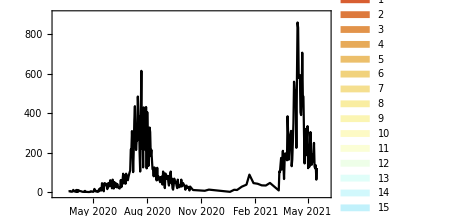
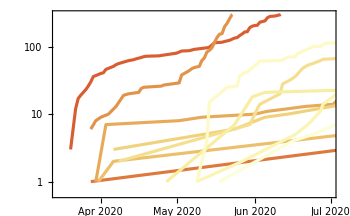
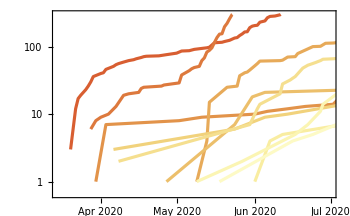
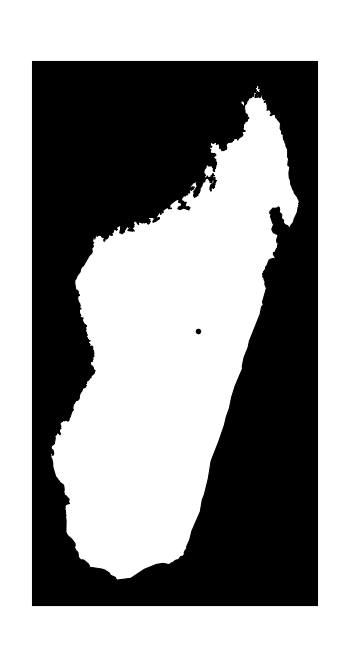
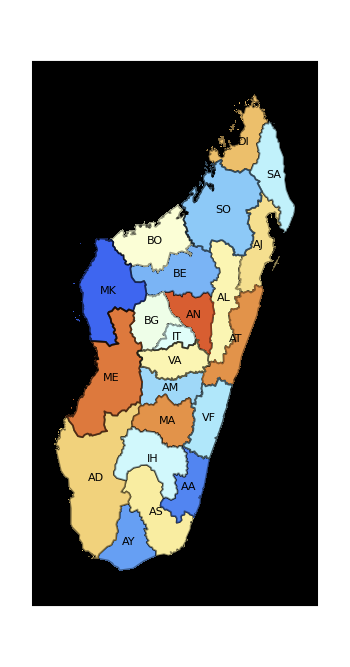
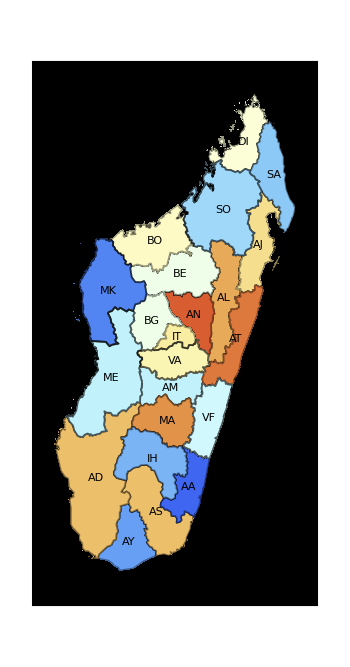
National level | 1^stcase | 5^thcase
-Graphics-New casesA) | -Graphics-Confirmed casesB) | -Graphics-Confirmed casesC)
-Graphics-D) | -Graphics-E) | -Graphics-F)

```mathematica
fig1 = Legended[Grid[Transpose@{{Style["National level",20,Black,Bold,FontFamily->"Helvetica"],f1x,road},{
 Style["1^stcase",20,Black,Bold,FontFamily->"Helvetica"],f1a,f1c},
{Style["5^thcase",20,Bold,Black,FontFamily->"Helvetica"],f1b,f1d}},
Spacings->{5,{5,1,5}}],lg1b]
```

```mathematica
Export["figs/figArrival.png", fig1, ImageResolution->150]
```

figs/figArrival.png

### Figure 2: Comparing mobility matrices

```mathematica
dmgr1 = Diagonal[Import["data/mobility_gravity_0.5.csv"]];
temp= AssociationThread[keyMob, dmgr1];
rankgr1 = RankFunction[1/temp];

dmgr2 = Diagonal[Import["data/mobility_gravity_1.csv"]];
temp = AssociationThread[keyMob, dmgr2];
rankgr2 = RankFunction[1/temp];

dmgr3 = Diagonal[Import["data/mobility_gravity_1.5.csv"]];
temp= AssociationThread[keyMob, dmgr3];
rankgr3= RankFunction[1/temp];

dmim = Diagonal[Import["data/mobility_imf.csv"]];
temp= AssociationThread[keyMob, dmim];
rankim = RankFunction[1/temp];

dmor = Diagonal[Import["data/mobility_orange.csv"]];
temp= AssociationThread[keyMob, dmor];
rankor= RankFunction[1/temp];

dmtr1 = Diagonal[Import["data/mobility_transit_0.5.csv"]];
temp= AssociationThread[keyMob, dmtr1];
ranktr1 = RankFunction[1/temp];

dmtr2 = Diagonal[Import["data/mobility_transit_1.csv"]];
temp = AssociationThread[keyMob, dmtr2];
ranktr2 = RankFunction[1/temp];

dmtr3 = Diagonal[Import["data/mobility_transit_1.5.csv"]];
temp= AssociationThread[keyMob, dmtr3];
ranktr3= RankFunction[1/temp];
```

```mathematica
CorrTest[rankgr3, ranktr3]
```

{0.884,0.}

```mathematica
CorrTest[rankgr3, rankim]
```

{0.982,0.}

```mathematica
CorrTest[ranktr3, rankim]
```

{0.878,0.}

```mathematica
CorrTest[rankgr3, rankor]
```

{0.261,0.24}

```mathematica
CorrTest[rankim, rankor]
```

{0.277,0.212}

```mathematica
rankgr1MX = KeyMap[# /.geoKey &, rankgr1];
rankgr1MX = Table[admin2Mada[[i]] -> COL[[rankgr1MX[admin2Mada[[i,2,1]]]]],{i, Length@admin2Mada}];
rankgr2MX = KeyMap[# /.geoKey &, rankgr2];
rankgr2MX = Table[admin2Mada[[i]] -> COL[[rankgr2MX[admin2Mada[[i,2,1]]]]],{i, Length@admin2Mada}];
rankgr3MX = KeyMap[# /.geoKey &, rankgr3];
rankgr3MX = Table[admin2Mada[[i]] -> COL[[rankgr3MX[admin2Mada[[i,2,1]]]]],{i, Length@admin2Mada}];

rankimMX = KeyMap[# /.geoKey &, rankim];
rankimMX = Table[admin2Mada[[i]] -> COL[[rankimMX[admin2Mada[[i,2,1]]]]],{i, Length@admin2Mada}];
rankorMX = KeyMap[# /.geoKey &, rankor];
rankorMX = Table[admin2Mada[[i]] -> COL[[rankorMX[admin2Mada[[i,2,1]]]]],{i, Length@admin2Mada}];

ranktr1MX = KeyMap[# /.geoKey &, ranktr1];
ranktr1MX = Table[admin2Mada[[i]] -> COL[[ranktr1MX[admin2Mada[[i,2,1]]]]],{i, Length@admin2Mada}];
ranktr2MX = KeyMap[# /.geoKey &, ranktr2];
ranktr2MX = Table[admin2Mada[[i]] -> COL[[ranktr2MX[admin2Mada[[i,2,1]]]]],{i, Length@admin2Mada}];
ranktr3MX = KeyMap[# /.geoKey &, ranktr3];
ranktr3MX = Table[admin2Mada[[i]] -> COL[[ranktr3MX[admin2Mada[[i,2,1]]]]],{i, Length@admin2Mada}];
```

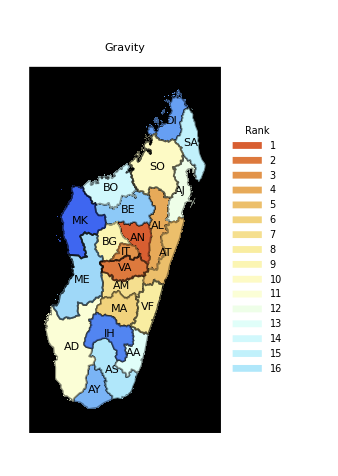
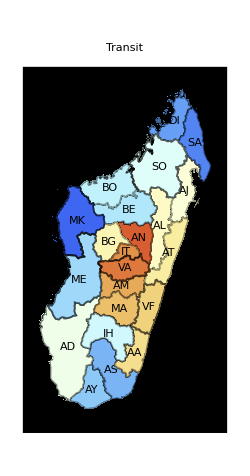
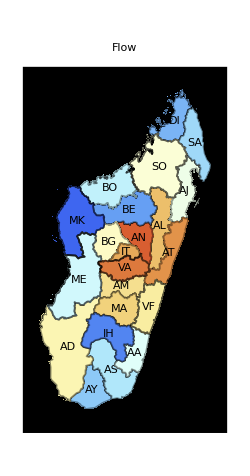
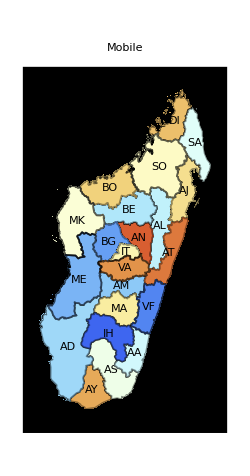
-Graphics-A) | -Graphics-B) | -Graphics-C) | -Graphics-D)

```mathematica
XX1 = { rankgr3MX,ranktr3MX, rankimMX, rankorMX};
lXX1= {"Gravity", "Transit", "Flow", "Mobile"};
l2XX1 = {"A)", "B)", "C)", "D)"};
fig2 = 
Legended[
Grid[
Partition[Table[
Labeled[GeoRegionValuePlot[XX1[[i]],
PlotStyle-> EdgeForm[{AbsoluteThickness[1.25],Black}],
PlotLabel-> Style[lXX1[[i]],18,Black], GeoBackground->None,PlotLegends->None, ImageSize->250,GeoLabels->Function[{polygon,entity,pos,data},{polygon,Black,Style[Text[ToCode[StringSplit[CommonName@entity,{","," County"}][[1]]],pos],8]}]],Style[l2XX1[[i]], 24, Black,FontFamily->"Helvetica"],{{Top,Left}}],{i,4}],4]
],lg1b]
```

```mathematica
Export["figs/figRankMob.png",fig2, ImageResolution-> 150]
```

figs/figRankMob.png

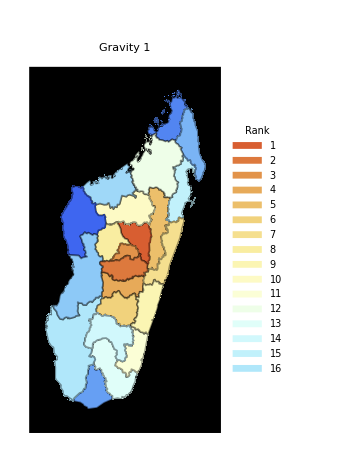
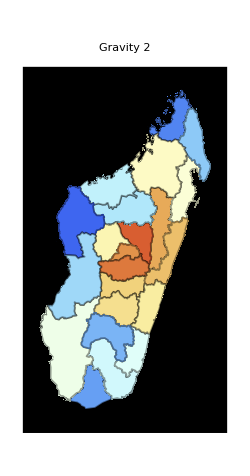
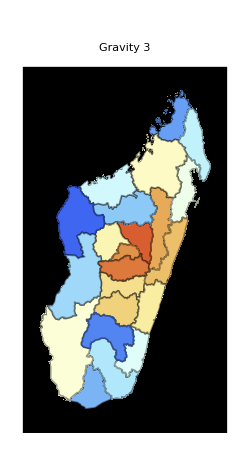
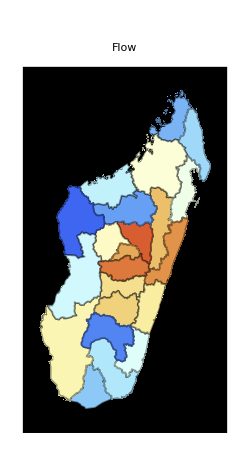
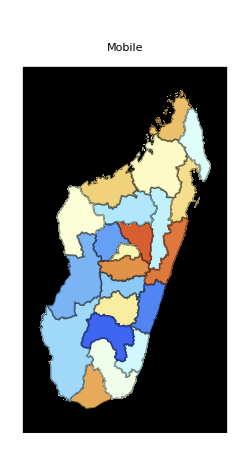
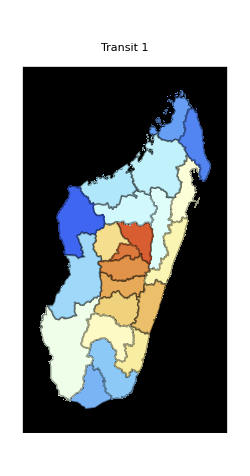
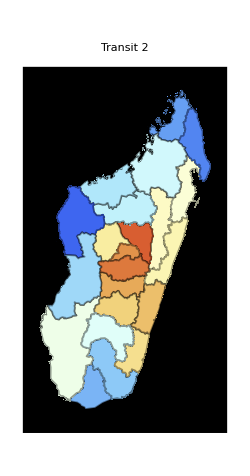
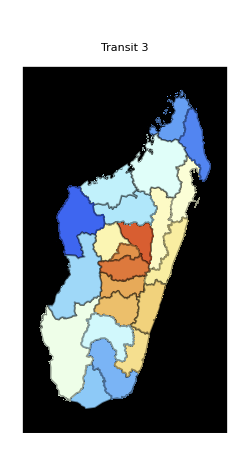
-Graphics-A) | -Graphics-B) | -Graphics-C) | -Graphics-D)
-Graphics-E) | -Graphics-F) | -Graphics-G) | -Graphics-H)

```mathematica
XX = {rankgr1MX,rankgr2MX, rankgr3MX, rankimMX, rankorMX,ranktr1MX,ranktr2MX, ranktr3MX};
lXX = {"Gravity 1", "Gravity 2", "Gravity 3", "Flow", "Mobile","Transit 1", "Transit 2", "Transit 3"};
l2XX = {"A)","B)","C)", "D)","E)","F)", "G)", "H)"};
figS1 = 
Legended[
Grid[
Partition[Table[Labeled[GeoRegionValuePlot[XX[[i]],
PlotStyle-> EdgeForm[{AbsoluteThickness[1.25],Black}],
PlotLabel-> Style[lXX[[i]],18,Black], GeoBackground->None,PlotLegends->None, ImageSize->250],Style[l2XX[[i]], 20, Black,FontFamily->"Helvetica"],{{Top,Left}}],{i,8}],4]
],lg1b]
```

```mathematica
Export["figs/figMobMatrix.png",figS1, ImageResolution-> 150]
```

figs/figMobMatrix.png

### Figure 3: true vs simulated

```mathematica
rank1
```

<|AN→1,ME→2,MA→3,AT→3,DI→5,AD→6,AJ→7,AS→8,VA→9,AL→9,BO→11,BG→12,IT→13,IH→14,SA→15,VF→16,AM→17,SO→18,BE→19,AY→20,AA→21,MK→22|>

```mathematica
keyMob = Import["data/mobility_gravity_raw_1.csv"][[2;;,1]]; 
nameMV = {"unif", "grav_0.5", "grav_1", "grav_1.5","imf","orange","tran_0.5", "tran_1","tran_1.5"}; 
time = 700;
```

```mathematica
REScorr1 = REScorr5= {};
RESquan51 = RESquan101= RESquan55 = RESquan105={};
Do[
inname = "data/sim_data/simMob_"<>nameMV[[MV]]<>"_diag_10000_rep_"<>ToString@rep<>"_time_"<>ToString@time<>".mx";
data = Import[inname];
simrank1  = Prepend[Table[LengthWhile[data[[All,3, i]], # ≤1 &] ,{i,2,22}],1];
simrank1 =RankFunction[AssociationThread[keyMob, simrank1]];

simrank5  = Prepend[Table[LengthWhile[data[[All,3, i]], # ≤5 &] ,{i,2,22}],1];
simrank5 =RankFunction[AssociationThread[keyMob, simrank5]];

temp1 = CorrTest[rank1, simrank1][[1]];
temp2 = CorrTest[rank5, simrank5][[1]];

temp3 = QuanTest[rank1,simrank1,6];
temp4 = QuanTest[rank5,simrank5,6];

temp5 = QuanTest[rank1,simrank1,11];
temp6 = QuanTest[rank5,simrank5,11];

AppendTo[REScorr1, temp1];
AppendTo[REScorr5, temp2];
AppendTo[RESquan51, temp3];
AppendTo[RESquan55, temp4];
AppendTo[RESquan101, temp5];
AppendTo[RESquan105, temp6];

,{MV, 9},{rep, 100}]
```

```mathematica
ip = ImagePadding-> {{30,10},{20,10}};
ip2 = ImagePadding-> {{20,10},{20,10}};
ipb = ImagePadding-> {{20,10},{40,10}};
```

```mathematica
lb2a = Style[#, 18, Black,FontFamily->"Helvetica"] &/@ {"Mobility matrix","Correlation"};
lb2b = Style[#, 18, Black,FontFamily->"Helvetica"] &/@ {"Mobility matrix","Overlap","Top five ranks"};
lb2c= Style[#, 18, Black,FontFamily->"Helvetica"] &/@ {"Mobility matrix","Overlap","Top ten ranks"};
```

```mathematica
lg2 = SwatchLegend[COL[[{2,-2}]],Style[#,16,Black,FontFamily->"Helvetica"]&/@{"1^st case","5^th case"},LegendLayout->"Row"]
```

```mathematica
VV = {1,4,9,5,6};
f2a =Labeled[
Labeled[
DistributionChart[Transpose[{Partition[REScorr1,100][[VV]],Partition[REScorr5,100][[VV]]}],ChartStyle->COL[[{1,-1}]],BarSpacing->{0.3,1.5}, ChartLabels->{{"N", "G","T","F", "M"},None(*{"1^st","5^th"}*)}, ls,is,fs,ip],
lb2a[[2]], {Left},RotateLabel->True],Style["B)", 24, Black,FontFamily->"Helvetica"],{{Top,Left}}];
```

```mathematica
Stat1[data_]:= Around[ Mean@data,{Min@data - Mean@data, Max@data- Mean@data}]
```

```mathematica
ps4 = PlotStyle->(Directive[#, AbsoluteThickness[3]]&/@COL[[{1,-1}]]);
ft = FrameTicks-> {{Automatic, None},{Transpose[{Range[5]+0.15,{"N", "G","T","F", "M"}}],None}};
dd1 = Transpose[{Range[5],Map[Stat1,Partition[RESquan51,100][[VV]]]}];
dd2 = Transpose[{Range[5]+0.3,Map[Stat1,Partition[RESquan55,100][[VV]]]}];
```

```mathematica
f2b = Labeled[Labeled[ListPlot[{dd1,dd2},PlotRange->{{0.5,5.35 +0.3},{-0.2,5.1}},PlotMarkers->{"◆",14},is,fs,ls,Frame->True,ps4, ft,ip],lb2b[[2]],{(*Bottom,*)Left(*,Top*)},RotateLabel->True],Style["A)", 24, Black,FontFamily->"Helvetica"],{{Top,Left}}];
```

```mathematica
dd3 = Transpose[{Range[5],Map[Stat1,Partition[RESquan101,100][[VV]]]}];
dd4 = Transpose[{Range[5]+0.3,Map[Stat1,Partition[RESquan105,100][[VV]]]}];
```

```mathematica
f2c = Labeled[Labeled[ListPlot[{dd3,dd4},PlotRange->{{0.5,5.35 +0.3},{-0.1,10.1}},PlotMarkers->{"◆",14},is,fs,ls,Frame->True,ps4, ft ,ip],lb2b[[2]],{Left(*,Top*)},RotateLabel->True],Style["C)", 24, Black,FontFamily->"Helvetica"],{{Top,Left}}];
```

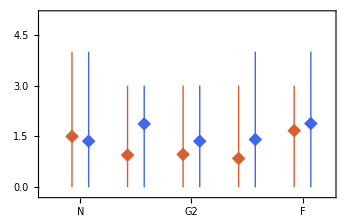
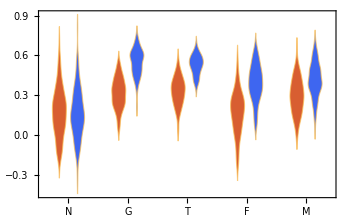
-Graphics-OverlapA) | -Graphics-CorrelationB)Mobility Matrix

```mathematica
fig3 = Labeled[Grid[{{f2b,f2a}}],{lg2,Style["Mobility Matrix", 20,Black, FontFamily->"Helvetica"]},{Top,Bottom},Spacings->{Automatic,Automatic}]
```

```mathematica
Export["figs/figCorrelation.png", fig3, ImageResolution->300]
```

figs/figCorrelation.png

```mathematica
fS2a =Labeled[Labeled[
DistributionChart[Transpose[{Partition[REScorr1,100],Partition[REScorr5,100]}],ChartStyle->COL[[{1,-1}]],BarSpacing->{0.3,1.5}, ChartLabels->{{"N", "G1", "G2", "G3","F", "M", "T1","T2","T3"},None(*{"1^st","5^th"}*)}, ls,is,fs,ip],
lb2a[[2]], {Left},RotateLabel->True],Style["C)", 24, Black,FontFamily->"Helvetica"],{{Top,Left}}];
```

```mathematica
Stat1[data_]:= Around[ Mean@data,{Min@data - Mean@data, Max@data- Mean@data}]
```

```mathematica
ps4 = PlotStyle->(Directive[#, AbsoluteThickness[3]]&/@COL[[{1,-1}]]);
ft = FrameTicks-> {{Automatic, None},{Transpose[{Range[6]+0.15,{"N", "G1", "G2", "G3","F", "M"}}],None}};
fts = FrameTicks-> {{Automatic, None},{Transpose[{Range[9]+0.15,{"N", "G1", "G2", "G3","F", "M", "T1","T2","T3"}}],None}};
```

```mathematica
dds1 = Transpose[{Range[9],Map[Stat1,Partition[RESquan51,100]]}];
dds2 = Transpose[{Range[9]+0.3,Map[Stat1,Partition[RESquan55,100]]}];
```

```mathematica
fS2b = Labeled[Labeled[ListPlot[{dds1,dds2},PlotRange->{{0.5,9.35 +0.3},{-0.2,5.1}},PlotMarkers->{"◆",14},is,fs,ls,Frame->True,ps4, fts,ip],lb2b[[2]],{Left},RotateLabel->True],Style["A)", 24, Black,FontFamily->"Helvetica"],{{Top,Left}}];
```

```mathematica
dds3 = Transpose[{Range[9],Map[Stat1,Partition[RESquan101,100]]}];
dds4 = Transpose[{Range[9]+0.3,Map[Stat1,Partition[RESquan105,100]]}];
```

```mathematica
fS2c =Labeled[ Labeled[ListPlot[{dds3,dds4},PlotRange->{{0.5,9.35 +0.3},{-0.2,10.2}},PlotMarkers->{"◆",14},is,fs,ls,Frame->True,ps4, fts ,ip],lb2b[[2]],{Left},RotateLabel->True],Style["B)", 24, Black,FontFamily->"Helvetica"],{{Top,Left}}];
```

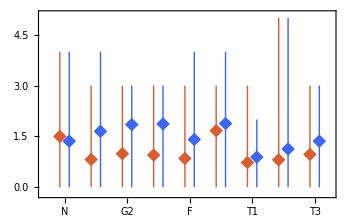
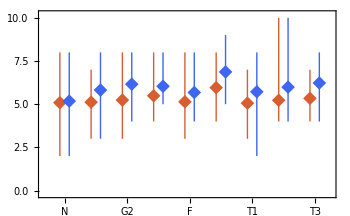
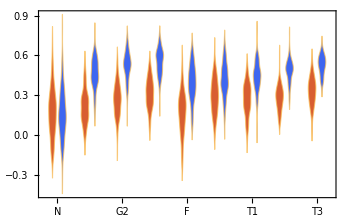
First five | First ten | 
-Graphics-OverlapA) | -Graphics-OverlapB) | -Graphics-CorrelationC)Mobility Matrix

```mathematica
figS3 = Labeled[Grid[{ {Style["First five",20,Black,FontFamily->"Helvetica"],Style["First ten",20,Black,FontFamily->"Helvetica"],""},{fS2b,fS2c,fS2a}}],{lg2,Style["Mobility Matrix", 20,Black, FontFamily->"Helvetica"]},{Top,Bottom},Spacings->{Automatic,1.5}]
```

```mathematica
Export["figs/figSuppCorrelation.png", figS3, ImageResolution->350]
```

figs/figSuppCorrelation.png

### Figure 4: RMSE

```mathematica
RMSE[sim_, true_]:= Module[{ll = sim[[1]]//Length, rmse, keyMob,result = {}},
keyMob = Keys[sim];
Do[
rmse = (sim[ky] - true[ky])^2/ll//Total// Sqrt//N;
AppendTo[result, ky ->rmse];
,{ky, keyMob}];
result = Sort[Association[result],"AN"];
result]
```

```mathematica
STD[sim_]:= Module[{ll = sim[[1]]//Length, std, keyMob,result = {}},
keyMob = Keys[sim];
Do[
std = StandardDeviation@sim[ky] //N;
AppendTo[result, ky ->std];
,{ky, keyMob}];
result = Sort[Association[result],"AN"];
result]
```

```mathematica
keyMob = Import["data/mobility_gravity_raw_1.csv"][[2;;,1]]; 
nameMV = {"unif", "grav_0.5", "grav_1", "grav_1.5","imf","orange","tran_0.5", "tran_1","tran_1.5"}; 
time = 700;
```

```mathematica
RANK1= RANK5 = {};
Do[
rep = 1;

inname = "data/sim_data/simMob_"<>nameMV[[MV]]<>"_diag_10000_rep_"<>ToString@rep<>"_time_"<>ToString@time<>".mx";
data = Import[inname];
simrank1  =Prepend[Table[LengthWhile[data[[All,3, i]], # ≤1 &] ,{i,2,22}],1];
simrank1 ={#}&/@ RankFunction[AssociationThread[keyMob, simrank1]];

simrank5  = Prepend[Table[LengthWhile[data[[All,3, i]], # ≤5 &] ,{i,2,22}],1];
simrank5 ={#}&/@RankFunction[AssociationThread[keyMob, simrank5]];

Do[
inname = "data/sim_data/simMob_"<>nameMV[[MV]]<>"_diag_10000_rep_"<>ToString@rep<>"_time_"<>ToString@time<>".mx";
data = Import[inname];
temp = Prepend[Table[LengthWhile[data[[All,3, i]], # ≤1 &] ,{i,2,22}],1];
temp =RankFunction[AssociationThread[keyMob, temp]];
AppendTo[simrank1[#], temp[#]]&/@keyMob;

temp  = Prepend[Table[LengthWhile[data[[All,3, i]], # ≤5 &] ,{i,2,22}],1];
temp =RankFunction[AssociationThread[keyMob, temp]];
AppendTo[simrank5[#], temp[#]]&/@keyMob;

,{rep, 2,100,1}];

AppendTo[RANK1, simrank1];
AppendTo[RANK5, simrank5];

,{MV, 9}];
```

#### RMSE

```mathematica
geoKey =AssociationThread[keysID[[All,-1]],keysID[[All,-2]]];
PL = {"Uniform", "Gravity 0.5", "Gravity 1", "Gravity 1.5", "Flow","Mobile", "Transit 0.5", "Transit 1", "Transit 1.5"};
PLs = {"Uniform", "Gravity", "Gravity", "Gravity", "Flow","Mobile", "Transit", "Transit", "Transit"};
```

```mathematica
res5 = Table[RMSE[RANK5[[i]],rank5],{i,9}];
dat5=Table[ Association@KeyMap[# /.geoKey &, res5[[i]]],{i,9}];
datr5= Table[Table[admin2Mada[[i]] -> dat5[[j]][admin2Mada[[i,2,1]]],{i, 2,Length@admin2Mada}],{j,9}];
MAX5 = datr5//Values//Flatten//Max;
```

```mathematica
lg4 = BarLegend[{(ColorData["SunsetColors"][(MAX5 -#)/MAX5]&),{0,MAX5}},LegendLabel->Style["RMSE",18,Black, FontFamily->"Helvetica"], LabelStyle->Directive[14,Black,FontFamily->"Helvetica"]]
```

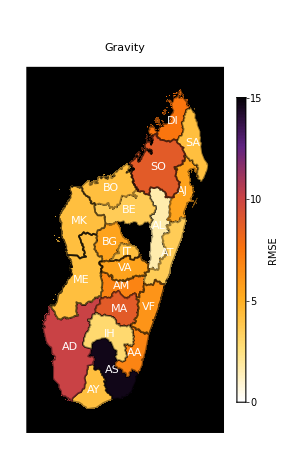
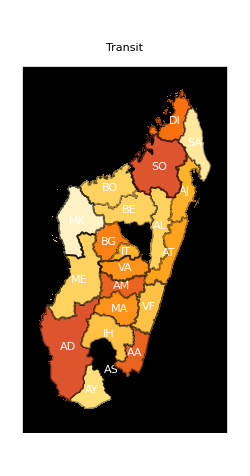
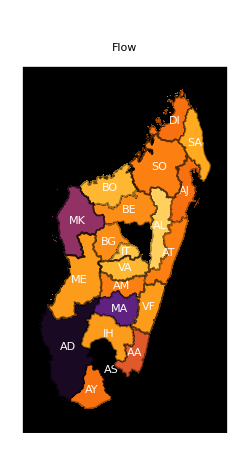
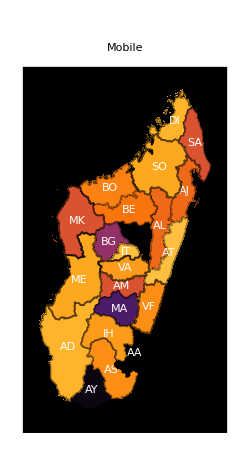
-Graphics-A) | -Graphics-B) | -Graphics-C) | -Graphics-D)

```mathematica
II ={4,9,5,6};
fig4 = 
Legended[
Grid[
{Table[
Labeled[GeoRegionValuePlot[datr5[[II[[i]]]],ColorFunction->(ColorData["SunsetColors"][(MAX5 -#)/MAX5]&),PlotStyle-> EdgeForm[{AbsoluteThickness[1.25],Black}],PlotLabel-> Style[PLs[[II[[i]]]],18,Black], GeoBackground->None,PlotLegends->None, ImageSize->250,ColorFunctionScaling->False,
GeoLabels->Function[{polygon,entity,pos,data},{polygon,White,Style[Text[ToCode[StringSplit[CommonName@entity,{","," County"}][[1]]],pos],8]}]],Style[l2XX[[i]], 24, Black,FontFamily->"Helvetica"],{{Top,Left}}]
,{i,4}]}]
,lg4]
```

```mathematica
Export["figs/figRMSE5.png", fig4, ImageResolution->150]
```

figs/figRMSE5.png

```mathematica
res1 = Table[RMSE[RANK1[[i]],rank1],{i,9}];
dat1=Table[ Association@KeyMap[# /.geoKey &, res1[[i]]],{i,9}];
datr1= Table[Table[admin2Mada[[i]] -> dat1[[j]][admin2Mada[[i,2,1]]],{i,2, Length@admin2Mada}],{j,9}];
MAX1 = datr1//Values//Flatten//Max;
```

```mathematica
lg3 = BarLegend[{(ColorData["SunsetColors"][(MAX1 -#)/MAX1]&),{0,MAX1}},LegendLabel->Style["RMSE",18,Black, FontFamily->"Helvetica"], LabelStyle->Directive[14,Black,FontFamily->"Helvetica"]]
```

```mathematica
fig3 = 
Legended[
Grid[
{Table[
Labeled[GeoRegionValuePlot[datr1[[II[[i]]]],ColorFunction->(ColorData["SunsetColors"][(MAX1 -#)/MAX1]&),PlotStyle-> EdgeForm[{AbsoluteThickness[1.25],Black}],PlotLabel-> Style[PLs[[II[[i]]]],18,Black], GeoBackground->None,PlotLegends->None, ImageSize->250,ColorFunctionScaling->False,
GeoLabels->Function[{polygon,entity,pos,data},{polygon,White,Style[Text[ToCode[StringSplit[CommonName@entity,{","," County"}][[1]]],pos],8]}]],Style[l2XX[[i]], 24, Black,FontFamily->"Helvetica"],{{Top,Left}}]
,{i,4}]}]
,lg3]
```

-Graphics-A) | -Graphics-B) | -Graphics-C) | -Graphics-D)

```mathematica
Export["figs/figRMSE1.png", fig3, ImageResolution->150]
```

figs/figRMSE1.png